```mathematica
(* In this script, the neutrino fluxes are calculated and plotted for the three initial conditions considered in the mnaucript. 
Notation wise, NH=Normal Hierarchy, IH=Inverted Hierarchy,EU=Early Universe and LU=Late Universe. We start by listing the parameters needed, which are retrieved from the ``Review of Particle Physics'', reference [32] of the manuscript.*)
```

```mathematica
Co[x_]:=Cos[x];
S[x_]:=Sin[x];
(*This is Subscript[θ, 12]*)
a=ArcSin[Sqrt[0.307]];
(*This is Subscript[θ, 13]*)
b=ArcSin[Sqrt[0.0218]];
(*This is Subscript[θ, 23] in the NH*)
NHc=ArcSin[Sqrt[0.545]];
(*This is Subscript[θ, 23] in the IH*)
IHc=ArcSin[Sqrt[0.547]];
(*CP violating phase δ*)
d=1.36*Pi;
(*Subscript[Δm, 21]^2=Subscript[m, 2]^2-Subscript[m, 1]^2*)
Dm21=7.53;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the IH*)
Dm32IH=-2.546;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the NH*)
Dm32NH=2.453;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the NH*)
Dm31NH=Dm32NH+Dm21;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the IH*)
Dm31IH=Dm32IH+Dm21;
(*This is a typical neutrino energy detected at neutrino observatories. As long as the value is high enough to be in the ultra-high energy regime, the excat value does not affect the results*)
E0=10^16.;
(*In natural units, Subscript[H, 0]=2.13 x10^-33 xh. We keep this infinitesimal prefactor seperate to better study the effect of choosing different h. In reality 
this prefactor can be cast away by a renormalization of the scale factor and redshift*)
H0=2.13*10^-33.;
(*Matter density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, m0]*)
Om0=0.315;
(*Dark Energy(DE) density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, Λ0]*)
Ol0=0.685;
(*Hubble parameter at EU, i.e. h^EU*)
EUh=0.675;
(*Hubble parameter at LU, i.e. h^LU*)
LUh=0.732;
(*This is the integrand in eq.(11) of the mansucript*)
Subscript[F, Λ][z_]:= (Om0*(1+z)^7.+Ol0*(1+z)^4.)^-.5;
int=Assuming[z>=0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]];
(*This is Δλ of the mnasucript, eq.(11), for EU*)
EUomAn=int/EUh;
(*This is Δλ of the mnasucript, eq.(11), for LU*)
LUomAn=int/LUh;
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
NHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[NHc]-S[b]*S[NHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[NHc]-S[a]*S[NHc]*S[b]*(Co[d]+I*S[d]),S[NHc]*Co[b]},{S[a]*S[NHc]-S[b]*Co[a]*Co[NHc]*(Co[d]+I*S[d]),-S[NHc]*Co[a]-S[a]*S[b]*Co[NHc]*(Co[d]+I*S[d]),Co[b]*Co[NHc]}};
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
IHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[IHc]-S[b]*S[IHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[IHc]-S[a]*S[IHc]*S[b]*(Co[d]+I*S[d]),S[IHc]*Co[b]},{S[a]*S[IHc]-S[b]*Co[a]*Co[IHc]*(Co[d]+I*S[d]),-S[IHc]*Co[a]-S[a]*S[b]*Co[IHc]*(Co[d]+I*S[d]),Co[b]*Co[IHc]}};
```

```mathematica
(*U^† for NH*)
NHUdag=ConjugateTranspose[NHU];
MatrixForm[NHUdag]
(*U^† for IH*)
IHUdag=ConjugateTranspose[IHU];
```

(0.823342 | -0.33511-0.0821029 ⅈ | 0.444342-0.0750181 ⅈ
0.548003 | 0.587244-0.0546464 ⅈ | -0.591065-0.0499308 ⅈ
-0.0628656-0.133596 ⅈ | 0.73015 | 0.667144)

```mathematica
(*The fllowing two lines are to check the Unitarity condition of the PMNS matrix, to make sure there was no error in writing them, for both NH and IH*)
```

```mathematica
MatrixForm[FullSimplify[NHUdag . NHU]];
MatrixForm[FullSimplify[IHUdag . IHU]];
```

```mathematica
(*The set of initial transition amplitudes conditions, Ψ^ini considered in the mansucript, ND, MD and PD, compactified in one matrix*)
TPsi0={{1,0,0},{0,1,0},{1/Sqrt[5],2/Sqrt[5],0}};
MatrixForm[TPsi0]
```

(1 | 0 | 0
0 | 1 | 0
1/(√5) | 2/(√5) | 0)

```mathematica
(*Initial transition amplitudes conditions in the mass basis, Φ of the manuscript, in the NH. Basically eq.(8) of the manuscript*)
TNHPhi0={NHUdag . TPsi0[[1]],NHUdag . TPsi0[[2]],NHUdag . TPsi0[[3]]};
MatrixForm[TNHPhi0]
(*Initial transition amplitudes conditions in the mass basis, Φ of the manuscript, in the IH. Basically eq.(8) of the manuscript*)
TIHPhi0={IHUdag . TPsi0[[1]],IHUdag . TPsi0[[2]],IHUdag . TPsi0[[3]]};
MatrixForm[TIHPhi0]
```

(0.823342+0. ⅈ | 0.548003+0. ⅈ | -0.0628656-0.133596 ⅈ
-0.33511-0.0821029 ⅈ | 0.587244-0.0546464 ⅈ | 0.73015+0. ⅈ
0.0684785-0.0734351 ⅈ | 0.770321-0.0488772 ⅈ | 0.624952-0.059746 ⅈ)

(0.823342+0. ⅈ | 0.548003+0. ⅈ | -0.0628656-0.133596 ⅈ
-0.334217-0.0822534 ⅈ | 0.586055-0.0547465 ⅈ | 0.731488+0. ⅈ
0.0692774-0.0735697 ⅈ | 0.769258-0.0489668 ⅈ | 0.626149-0.059746 ⅈ)

```mathematica
(*The evolving factors for the mass basis transition amplitudes, as written in eq.(10) of the mnasucript*)
```

```mathematica
T=DiagonalMatrix[{Co[m1^2*Intz/2]-I*S[m1^2*Intz/2],Co[m2^2*Intz/2]-I*S[m2^2*Intz/2],Co[m3^2*Intz/2]-I*S[m3^2*Intz/2]}];
(*The evolved transition amplitude, in the mass basis, with redshift, as given in eq.(10) of the mansucript, for NH*)
TNHPhi=FullSimplify[{T.TNHPhi0[[1]],T.TNHPhi0[[2]],T.TNHPhi0[[3]]}];
MatrixForm[TNHPhi]
(*The evolved transition amplitude, in the mass basis, with redshift, as given in eq.(10) of the mansucript, for IH*)
TIHPhi=FullSimplify[{T.TIHPhi0[[1]],T.TIHPhi0[[2]],T.TIHPhi0[[3]]}];
MatrixForm[TIHPhi]
```

(0.823342 ⅇ^(-1/2 ⅈ Intz m1^2) | 0.548003 ⅇ^(-1/2 ⅈ Intz m2^2) | (-0.0628656-0.133596 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2)
(-0.33511-0.0821029 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.587244-0.0546464 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | 0.73015 ⅇ^(-1/2 ⅈ Intz m3^2)
(0.0684785-0.0734351 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.770321-0.0488772 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | (0.624952-0.059746 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2))

(0.823342 ⅇ^(-1/2 ⅈ Intz m1^2) | 0.548003 ⅇ^(-1/2 ⅈ Intz m2^2) | (-0.0628656-0.133596 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2)
(-0.334217-0.0822534 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.586055-0.0547465 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | 0.731488 ⅇ^(-1/2 ⅈ Intz m3^2)
(0.0692774-0.0735697 ⅈ) ⅇ^(-1/2 ⅈ Intz m1^2) | (0.769258-0.0489668 ⅈ) ⅇ^(-1/2 ⅈ Intz m2^2) | (0.626149-0.059746 ⅈ) ⅇ^(-1/2 ⅈ Intz m3^2))

```mathematica
(*The evolved transition amplitude, in the flavor basis, with redshift, as given in eq.(10) of the mansucript, for NH*)
TNHPsi={NHU . TNHPhi[[1]],NHU . TNHPhi[[2]],NHU . TNHPhi[[3]]};
MatrixForm[TNHPsi];
(*The evolved transition amplitude, in the flavor basis, with redshift, as given in eq.(10) of the mansucript, for IH*)
TIHPsi={IHU . TIHPhi[[1]],IHU . TIHPhi[[2]],IHU . TIHPhi[[3]]};
MatrixForm[TNHPsi];
(*Here we present analytical expression for the total flux from all initial conditions for each neutrino flavor, in both hierarchies*)
(*On the techinical side, the flux of a certain flavor, as argued in the manuscript, is simply the sum of transition probabilities to that flavor, which is the modulus squared of transition amplitudes. This is what we are calculating below*)
Print["NHFlux-e="]
(*Subscript[ν, e] flux for NH*)
NHFluxe=FullSimplify[TrigReduce[ComplexExpand[Re[TNHPsi[[All,1]]]^2+Im[TNHPsi[[All,1]]]^2]]];
MatrixForm[NHFluxe]
Print["IHFluxe="]
(*Subscript[ν, e] flux for IH*)
IHFluxe=FullSimplify[TrigReduce[ComplexExpand[Re[TIHPsi[[All,1]]]^2+Im[TIHPsi[[All,1]]]^2]]];
MatrixForm[IHFluxe]
Print["NHFluxmu="]
(*Subscript[ν, μ] flux for NH*)
NHFluxmu=FullSimplify[TrigReduce[ComplexExpand[Re[TNHPsi[[All,2]]]^2+Im[TNHPsi[[All,2]]]^2]]];
MatrixForm[NHFluxmu]
Print["IHFluxmu="]
(*Subscript[ν, μ] flux for IH*)
IHFluxmu=FullSimplify[TrigReduce[ComplexExpand[Re[TIHPsi[[All,2]]]^2+Im[TIHPsi[[All,2]]]^2]]];
MatrixForm[IHFluxmu]
Print["NHFluxtau="]
(*Subscript[ν, τ] flux for NH*)
NHFluxtau=FullSimplify[TrigReduce[ComplexExpand[Re[TNHPsi[[All,3]]]^2+Im[TNHPsi[[All,3]]]^2]]];
MatrixForm[NHFluxtau]
Print["IHFluxtau="]
(*Subscript[ν, τ] flux for IH*)
IHFluxtau=FullSimplify[TrigReduce[ComplexExpand[Re[TIHPsi[[All,3]]]^2+Im[TIHPsi[[All,3]]]^2]]];
MatrixForm[IHFluxtau]
```

NHFlux-e=

(0.550198+0.407152 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0295561 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.0130934 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.196777-0.173533 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0121414 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0353854 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0600332 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0600332 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0600332 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.194345+0.0508403 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0140805 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0311048 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0480265 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00605253 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0719836 Sin[1/2 Intz (m2-m3) (m2+m3)])

IHFluxe=

(0.550198+0.407152 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0295561 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.0130934 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.196016-0.172687 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0120718 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0354011 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0600109 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0600109 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0600109 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.193977+0.0513411 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0141689 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.031149 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0480087 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00616949 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0720097 Sin[1/2 Intz (m2-m3) (m2+m3)])

NHFluxmu=

(0.196777-0.173533 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0121414 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0353854 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0600332 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0600332 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0600332 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.41938+0.0828138 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.126924 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.370882 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.418559-0.0145874 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0180778 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.414106 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0279657 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0261133 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0519228 Sin[1/2 Intz (m2-m3) (m2+m3)])

IHFluxmu=

(0.196016-0.172687 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0120718 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0354011 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0600109 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0600109 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0600109 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.420373+0.0820873 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.126777 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.370762 Cos[1/2 Intz (m2-m3) (m2+m3)]
0.418753-0.0146994 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0183137 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.41426 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0279293 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0262489 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0519304 Sin[1/2 Intz (m2-m3) (m2+m3)])

NHFluxtau=

(0.253024-0.233619 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0416975 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.022292 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0600332 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0600332 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0600332 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.383843+0.0907196 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.139066 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.335496 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0600332 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0600332 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0600332 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.387096-0.0362529 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0321582 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.383001 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0200608 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0200608 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0200608 Sin[1/2 Intz (m2-m3) (m2+m3)])

IHFluxtau=

(0.253786-0.234466 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0416279 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.0223077 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.0600109 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.0600109 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0600109 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.383611+0.0905995 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.138849 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.335361 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0600109 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0600109 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0600109 Sin[1/2 Intz (m2-m3) (m2+m3)]
0.38727-0.0366417 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0324826 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.383111 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0200794 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0200794 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0200794 Sin[1/2 Intz (m2-m3) (m2+m3)])

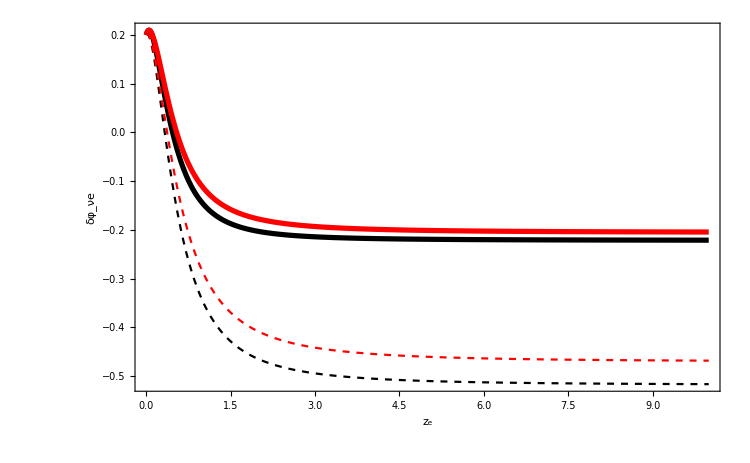

```mathematica
(*After having calculated the general analytixal expressions, we now specify to the two cases of EU and LU and plot each of their evolution with redshift*)
(*Subscript[ν, e] flux for NH-EU*)
NHTotFluxeEU[z_]=Total[NHFluxe]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*EUomAn};
(*Subscript[ν, e] flux for NH-LU*)
NHTotFluxeLU[z_]=Total[NHFluxe]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*LUomAn};
(*Subscript[ν, e] flux for IH-EU*)
IHTotFluxeEU[z_]=Total[IHFluxe]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*EUomAn};
(*Subscript[ν, e] flux for IH-LU*)
IHTotFluxeLU[z_]=Total[IHFluxe]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*LUomAn};
(*Here we plot the fractional difference between emmitted and observed fluxes, as explained in eq.(15) of the manuscript*)
Plot[{NHTotFluxeEU[z]-1,NHTotFluxeLU[z]-1,IHTotFluxeEU[z]-1,IHTotFluxeLU[z]-1},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_νe",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

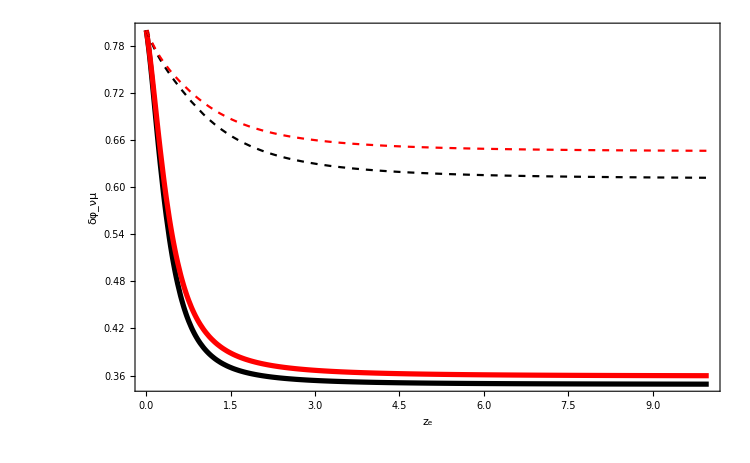

```mathematica
(*Subscript[ν, μ] flux for NH-EU*)
NHTotFluxmuEU[z_]=Total[NHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*EUomAn};
(*Subscript[ν, μ] flux for NH-LU*)
NHTotFluxmuLU[z_]=Total[NHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*LUomAn};
(*Subscript[ν, μ] flux for IH-EU*)
IHTotFluxmuEU[z_]=Total[IHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*EUomAn};
(*Subscript[ν, μ] flux for IH-LU*)
IHTotFluxmuLU[z_]=Total[IHFluxmu]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*LUomAn};
Plot[{NHTotFluxmuEU[z]-1,NHTotFluxmuLU[z]-1,IHTotFluxmuEU[z]-1,IHTotFluxmuLU[z]-1},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_νμ",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

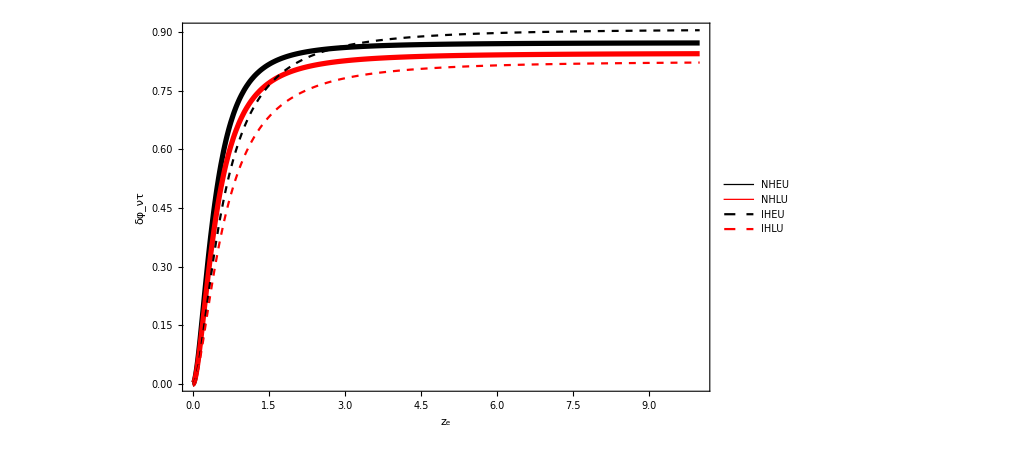

```mathematica
(*Subscript[ν, τ] flux for NH-EU*)
NHTotFluxtauEU[z_]=Total[NHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*EUomAn};
(*Subscript[ν, τ] flux for NH-LU*)
NHTotFluxtauLU[z_]=Total[NHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31NH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32NH*LUomAn};
(*Subscript[ν, τ] flux for IH-EU*)
IHTotFluxtauEU[z_]=Total[IHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*EUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*EUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*EUomAn};
(*Subscript[ν, τ] flux for IH-LU*)
IHTotFluxtauLU[z_]=Total[IHFluxtau]/.{(m1-m2)*(m1+m2)*Intz->- Dm21*LUomAn,(m1-m3)*(m1+m3)*Intz->-Dm31IH*LUomAn,(m2-m3)*(m2+m3)*Intz->-Dm32IH*LUomAn};
Plot[{NHTotFluxtauEU[z],NHTotFluxtauLU[z],IHTotFluxtauEU[z],IHTotFluxtauLU[z]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["NHEU",24],Style["NHLU",24],Style["IHEU",24],Style["IHLU",24]},{Right,Bottom}],FrameLabel->{Style["z_e",24,Bold],Style["δφ_ντ",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],22,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

```mathematica
(*Here we plot the fractional differnce between EU and LU for each flux, as given in eq.(16) of the mansucript*)
```

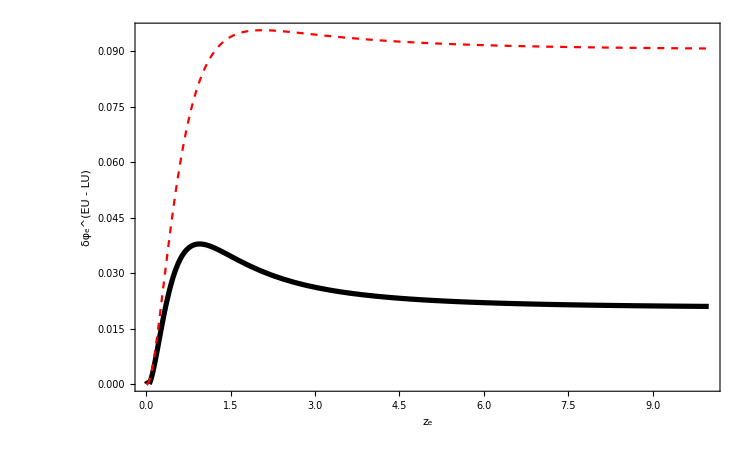

```mathematica
Plot[{Abs[(NHTotFluxeEU[z]-NHTotFluxeLU[z])/Max[NHTotFluxeEU[z],NHTotFluxeLU[z]]],Abs[(IHTotFluxeEU[z]-IHTotFluxeLU[z])/Max[IHTotFluxeEU[z],IHTotFluxeLU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_e^(EU - LU)",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

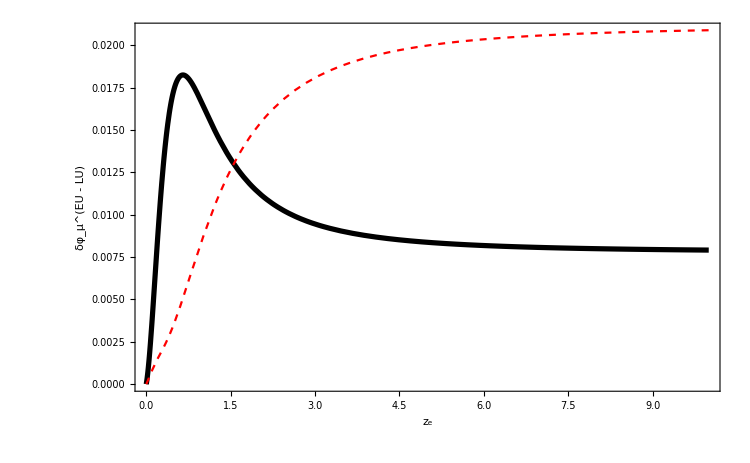

```mathematica
Plot[{Abs[(NHTotFluxmuEU[z]-NHTotFluxmuLU[z])/Max[NHTotFluxmuEU[z],NHTotFluxmuLU[z]]],Abs[(IHTotFluxmuEU[z]-IHTotFluxmuLU[z])/Max[IHTotFluxmuEU[z],IHTotFluxmuLU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},FrameLabel->{Style["z_e",24,Bold],Style["δφ_μ^(EU - LU)",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```

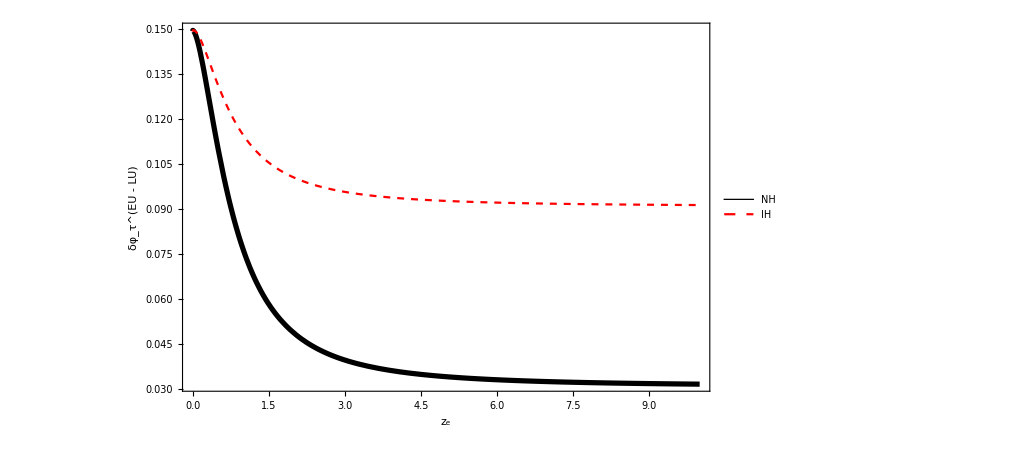

```mathematica
Plot[{Abs[(NHTotFluxtauEU[z]-NHTotFluxtauLU[z])/Max[NHTotFluxtauEU[z],NHTotFluxtauLU[z]]],Abs[(IHTotFluxtauEU[z]-IHTotFluxtauLU[z])/Max[IHTotFluxtauEU[z],IHTotFluxtauLU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->Placed[{Style["NH",24],Style["IH",24]},{Right,Top}],FrameLabel->{Style["z_e",24,Bold],Style["δφ_τ^(EU - LU)",24,Bold]},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],24,FontFamily->"Helvetica",Bold]]
(*Export["Path",%,name.pdf,"PDF"]*)
```